```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
Cov2={4,20,1,1,32,32,24,24,24,30,0,8,8,12,20,32,24};
Cov3={1,0,0.5,0.5,2,5,4.5,2.5,4,2,0,4,6,4,6,10,8};
Cov4=RandomReal[] Cov2;
Cov5=RandomReal[] Cov2;
```

```mathematica
(* Loop to generate failure counts *)
ω=55;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]],Cov2[[j]],Cov3[[j]],Cov4[[j]],Cov5[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->5,β->{0.21774224,0.03132722,0.17702043,0.01,0.01},h->GM/.{b->0.026192}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{0,4,4,1,4,1,2,0,1,0,1,3,0,0,1,0,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{0,4,8,9,13,14,16,16,17,17,18,21,21,21,22,22,22}

```mathematica
(* MLEs *)
h=GM;
lnLa=lnL/.{y-> FC,x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,β2]},{0==D[lnLa,β3]},{0==D[lnLa,β4]},{0==D[lnLa,β5]},{0==D[lnLa,b]}},{{ω,55},{β1,0.217},{β2,0.0313},{β3,0.177},{β4,0.01},{β5,0.01},{b,0.0261}},MaxIterations->100000]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{ω→1916.79,β1→-0.405265,β2→0.0674791,β3→-0.184411,β4→-0.0936446,β5→-0.0134414,b→0.00107898}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3]Exp[x4[[i]] β4]Exp[x5[[i]] β5]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]]β1]Exp[x2[[g]]β2]Exp[x3[[g]]β3]Exp[x4[[g]]β4]Exp[x5[[g]]β5])/.Rules/.{x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
];
HωList//N
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1.93465,5.97301,7.79907,9.68118,12.5158,13.7401,14.3622,14.7604,16.6684,17.268,18.6914,19.3961,19.7939,20.7079,21.5424,21.9463,21.9959}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 7
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 7
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

58.4033

64.2358

17.6457

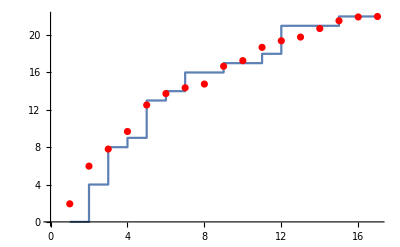

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red];(*,Joined->True,InterpolationOrder->4*)
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Intervals=Table[i,{i,1,17}];
If[AIC<65&&BIC<65&&SSE<35,Export["GM_5cov_sim.xlsx",Transpose[{Intervals,FC,Cov1,Cov2,Cov3, Cov4, Cov5}]]]
```

GM_5cov_sim.xlsx